## Generowanie funkcji G(x,y) określającej współczynnik rozpylenia dla punktu (x,y)

Jestem przyzwyczajony do używania znaków ⟦ i ⟧ zamiast [[ i ]], jest to dla mnie czytelniejsze. Wpisuje się je klawiszami escape [[ escape oraz escape ]] escape.

## Wartości stałe

### Rozmiar próbki (200nm x 200nm)

```mathematica
size=200;
```

### Liczba punktów będących zarodkami polikryształów

```mathematica
n=220*size*size/(200*200)
```

220

```mathematica
n
```

220

```mathematica
(* maksymalna liczba kroków *)
(*accuracy=80;*)
accuracy=80;
```

```mathematica
precision=10;
```

```mathematica
workingPrecision=17;
```

```mathematica
minPoints=1;(*IntegerPart[0.99*size]*)
```

```mathematica
maxPoints=200;
```

```mathematica
nomAngleInDegrees=0;
```

### Minimalna i maksymalna wartość współczynnika rozpylania

```mathematica
minSputter=0.7;
```

```mathematica
maxSputter = 1.2;
```

#### Kąt padania jonów

```mathematica
nomAngle=nomAngleInDegrees*Pi/180
```

0

### Czas trwania

```mathematica
(* 600s *)
```

```mathematica
tMax=600000000;
```

## Stworzenie tablicy G

Tu pobawiłem się trochę obsługą plików. Najpierw ustawiam ścieżkę obsługi plików z jakiejś domyślnej na tą gdzie znajduje się ten notebook. Potem jest zwykły if, w którym sprawdzam czy w tym folderze istnieje plik g_raw.dat i zmienna importGQ (czy chcę importować G z pliku) jest równa True. Jeśli tak to go importuję. Jeśli nie to otwieram plik erosion_G_new.nb (nie wiem czemu tutaj nie działa ścieżka ustawiona w SetDirectory dlatego cała konstrukcja z FileNameJoin), wykonuję go w całości i jak się wykona zamykam bez zapisu (dzięki temu outputy w pliku pierwotnym nie zmienią się).

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\lgaza\Dropbox\dissertation\ripple_formation\mathematica

```mathematica
importGQ=True;
```

```mathematica
If[
FileExistsQ[StringJoin["data/g_raw_", ToString[size],".dat"]]
&&FileExistsQ[StringJoin["data/seeds_",ToString[size],".dat"]]
&&FileExistsQ[StringJoin["data/sputter_coeffs_",ToString[size], ".dat"]]
&&importGQ,

G=Import[StringJoin["data/g_raw_", ToString[size],".dat"],"Table"];seeds=Import[StringJoin["data/seeds_",ToString[size],".dat"]]; sputterCoeffs=Import[StringJoin["data/sputter_coeffs_",ToString[size], ".dat"]];,

notebookG=NotebookOpen[FileNameJoin[{NotebookDirectory[],"prepare_data.nb"}]];
NotebookEvaluate[notebookG,InsertResults->True];
NotebookClose[notebookG];
]
```

## Dalsze obliczenia

### Przypisanie do poszczególnych krystalitów ich współczynników rozpylania

Używasz (szczególnie w obliczeniach G, które dałem do osobnego pliku) konstrukcji For, które nie są w Mathematice najwydajniejsze. Wszędzie tam gdzie chodzisz po liście można to zrobić funkcją Table, która jest dużo szybsza. Przepisałem twoje konstrukcje tak, żeby używały Table zapisując wyniki w zmiennych z dopisanym “2”. Żeby pokazać ci jakie są różnice w czasie wykonywania obu typów konstrukcji objąłem je funkcją AbsoluteTiming, która zwraca czas wykonywania instrukcji (całkowity, łącznie z czasem jaki jest potrzebny na wyświetlenie wyników, itp.).

```mathematica
G2=G;
```

```mathematica
AbsoluteTiming[
For[i=1,i≤size+1,++i,
For[j=1,j≤size+1,++j,
G[[i,j]]=1.0
(* Random sputter coeffs *)
(*G[[i,j]]=sputterCoeffs[[G[[i,j]]]][[1]]*)
(* Test 1 *)
(* All the same sputter coeff 1.0 *)
(*G[[i,j]]=1.0*)
(* Test 2 *)
(* Two sputter coeffs 0.7 and 1.2 *)
(*G[[i,j]]=If[i≤size/2,0.7,1.2]*)
]
]
]
```

{0.10845,Null}

```mathematica
i=.
j=.
k=.
```

```mathematica
(*AbsoluteTiming[
G2=Table[sputterCoeffs⟦G2⟦i,j⟧⟧,{i,size+1},{j,size+1}];
]*)
```

Zamiast Rotate wpisałem Reverse i Transpose czyli zamiast obracać obrazek (i przy okazji wszystkie osie, legendy, itp.) obróciłem dane.

```mathematica
G;
```

```mathematica
G[[1;;size,1;;size]];
```

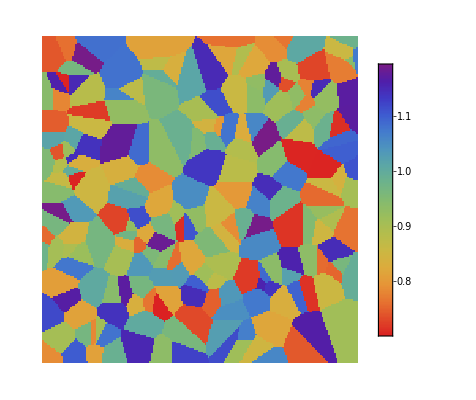

```mathematica
ArrayPlot[Reverse[Transpose[G[[1;;size,1;;size]]]], ColorFunction->(ColorData["Rainbow"][1-#]&), PlotLegends->Automatic]
```

Tutaj było clue problemu. Niestety Part (czyli ⟦ ⟧) nie może być wykonane jeśli indeksy nie są numeryczne. W Mathematice 10 wprowadzono funkcję Indexed, która robi dokładnie to co jest potrzebne czyli wyciąga coś z listy jeśli ma podane indeksy numeryczne a jak indeksy są symboliczne to pozostaje w formie abstrakcyjnej (symbolicznej). Jeśli chciałbyś mieć funkcję, która będzie działała we wcześniejszych wersjach to działać powinno rozwiązanie wykomentowane poniżej.

```mathematica
(*ListPart[x_List,spec__]:=x[[spec]];
Gfun2Old[x_,y_,t_]:=ListPart[G,Floor[x+1],Floor[y+1]]*)
```

```mathematica
(*mając tablicę G tworzę funkcję zwracającą wartość G dla pary(x,y)*)
Gfun[xparam_,yparam_,tparam_]:=G⟦Floor[xparam+1],Floor[yparam+1]⟧
```

```mathematica
Gfun2[xparam_,yparam_,tparam_]:=Indexed[G,{Floor[xparam+1],Floor[yparam+1]}]
```

```mathematica
Indexed[G,{Floor[2],Floor[3]}]
```

0.785312

### Ten sam rysunek (z użyciem tych samych zarodków ziaren, bez kolorowania) z użyciem VoronoiMesh - funkcji wbudowanej w Mathematicę

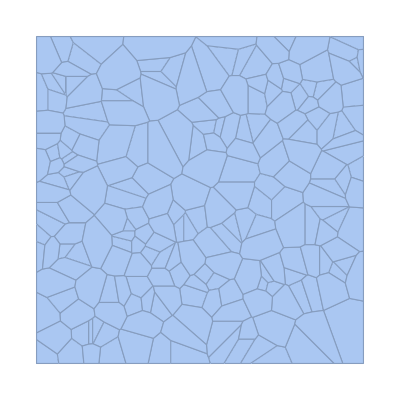

```mathematica
vor = VoronoiMesh[seeds, {{0, size+1}, {0,size+1}}]
```

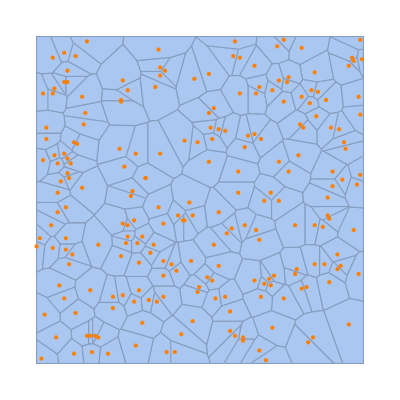

```mathematica
Show[%, Graphics[{Orange, Point[seeds]}]]
```

```mathematica
cells=MeshPrimitives[vor,2];
```

### Funkcja Yammamury

```mathematica
(* bierze pod uwagę zmianę współczynnika rozpylania spowodowaną zmianą lokalnego kąta padania strumienia *)
```

```mathematica
Y0=33/10; (* atom/jon współczynnik rozpylania dla strumienia padającego pod kątem prostym *)
```

```mathematica
f=195/100; (* bezwymiarowy współczynnik opisujący kształt zależności kątowej *)
```

#### Kąt dla którego współczynnik rozpylania jest największy

```mathematica
thOpt=70 * Pi/180
```

(7 π)/18

```mathematica
thOpt=70°
```

70 °

#### Definicja funkcji Yammamury

```mathematica
yammFormula[th_]:=Y0*Cos[th]^-f*Exp[f*(1-Cos[th]^-1)*Cos[thOpt]]
```

```mathematica
(* test funkcji Yammamury dla kątów od 0° do 90° *)
```

Wszystkie opisy osi, jeśli nie mają być pod nie podstawione zmienne, lepiej jest, żeby były wpisane jako string czyli otoczone cudzysłowami.

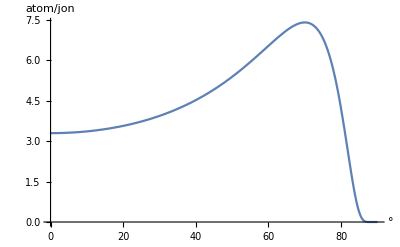

```mathematica
Plot[yammFormula[th Degree], {th,0,90},AxesLabel->{"°","atom/jon"}]
```

### Funkcja odpowiadająca za erozję powierzchni

```mathematica
Clear[h]
```

```mathematica
(* objętość atomu niklu *)
```

```mathematica
omega=1/(917/10);
```

```mathematica
(* strumień jonów *)
```

```mathematica
phi=7946/1000000000;
```

```mathematica
(* funkcja opisująca zależność cosinus lokalnego kąta padania od nominalnego kąta padania *)
```

Jako argument przekazujesz tylko nazwę funkcji, bez jej parametrów. Jeśli musiałbyś przekazać też bezpośrednio argumenty funkcji h to powinieneś je dodać jako zwykłe argumenty. Za to w samej funkcji zrobiłeś właściwie czyli musisz podać bezpośrednio wszystkie argumenty dla funkcji h.

```mathematica
cosThLocFormula[h_,x_,y_,t_,thNom_]:=(Sin[thNom]*D[h[x,y,t],x]+Cos[thNom])/Sqrt[D[h[x,y,t],y]^2+1+D[h[x,y,t],x]^2]
```

```mathematica
(* funkcja opisująca cosinus kąta pomiędzy normalną do lokalnej płaszczyzny a normalną do średniej płaszczyzny *)
```

```mathematica
cosThOffFormula[h_,x_,y_,t_]:=1/Sqrt[D[h[x,y,t],y]^2+1+D[h[x,y,t],x]^2]
```

```mathematica
EFormula[h_,x_,y_,t_,thNom_]:=-omega*phi*cosThLocFormula[h,x,y,t,thNom]/cosThOffFormula[h,x,y,t]*yammFormula[ArcCos[cosThLocFormula[h,x,y,t,thNom]]]*Gfun2[x,y,t]
```

### Równanie ewolucji powierzchni

```mathematica
Clear[x]
```

```mathematica
Clear[y]
```

```mathematica
Clear[t]
```

```mathematica
nomAngle
```

0

```mathematica
pde=D[h[x,y,t],t]==EFormula[h, x,y,t,nomAngle];
```

```mathematica
BConds = {h[0,y,t]==h[size,y,t],h[x,0,t]==h[x,size,t]}
```

{h[0,y,t]==h[200,y,t],h[x,0,t]==h[x,200,t]}

```mathematica
(* stożek??? *)
```

```mathematica
topographySimple[x1_,x2_]=If[x1≤size/4 , 0, If[x1<size/2,(400/size*x1-100),If[x1<3*size/4, (300-400/size*x1), 0]]]
```

If[x1≤50,0,If[x1<size/2,(400 x1)/size-100,If[x1<(3 size)/4,300-(400 x1)/size,0]]]

Zamiast takiego If można w Mathematice użyć Piecewise, które powinno działać razem z większą ilością funkcji i jest trochę czytelniejsze.

```mathematica
(* Niepłaska powierzchnia początkowa *)
```

```mathematica
size
```

200

```mathematica
topography[x1_,x2_]=Piecewise[{{(400/size*x1-100),size/4<x1<size/2},{(300-400/size*x1),size/2<x1<3*size/4},{100, x1==size/2},{0, x1≤size/4},{0, x1≥3*size/4}}];
```

```mathematica
topographyAlongY[x1_,x2_]=Piecewise[{{(400/size*x2-100),size/4<x2<size/2},{(300-400/size*x2),size/2<x2<3*size/4},{100, x2==size/2},{0, x2≤size/4},{0, x2≥3*size/4}}];
```

```mathematica
(*(*topography[x,y]*) (*400-400/199*x*)*)
```

```mathematica
(*ICond=h[x,y,0]==topographyAlongY[x,y];*)
```

```mathematica
ICond=h[x,y,0]==topography[x,y];
```

```mathematica
(*Płaska powierzchnia początkowa *)
```

```mathematica
(*ICond=h[x,y,0]==0;*)
```

```mathematica
size
```

200

```mathematica
(*sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100}}]*)
```

```mathematica
sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax},AccuracyGoal->accuracy,PrecisionGoal->precision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->minPoints,"MaxPoints"->maxPoints}},WorkingPrecision->workingPrecision,InterpolationOrder->All]
```

{{h→                                                                                                              8
InterpolatingFunction[{{…, 0, 200.00000000000000, …}, {…, 0, 200.00000000000000, …}, {0, 6.0000000000000000 10 }}, <>]}}

```mathematica
(*sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax}]*)
```

```mathematica
IntegerPart[0.9*size]
```

180

```mathematica
ffun[x_,y_,t_]:=h[x,y,t]/.sol⟦1⟧
```

```mathematica
ffun[150,150,1000000]
```

-0.2608486245713963

```mathematica
Manipulate[ContourPlot[ffun[x,y,t],{x,0,size},{y,0,size},ColorFunction->(ColorData["Rainbow"][1#]&), PlotLegends->Automatic],{t,0,tMax}]
```

```mathematica
tMax
```

600000000

```mathematica
Plot3D[Evaluate@Table[ffun[x,y,t], {t,{tMax}}],{x,0,size},{y,0,size},ColorFunction->"Rainbow",PlotLegends->Automatic, AxesLabel->{"nm","nm","nm"}]
```

-Graphics3D-

```mathematica
(*Wykres dla czasu t=0 (czerwony) i dla czasu t=tMax (zielony) *)
```

```mathematica
Manipulate[Plot3D[Evaluate@Table[ffun[x,y,t], {t,{time,tMax}}],{x,0,size},{y,0,size},PlotStyle->{Red,Green},PlotLegends->Automatic,AxesLabel->{"nm","nm","nm"},PlotRange->{{0,size},{0,size},{-20,100}}],{time,0,tMax}]
```

```mathematica
Plot3D[Evaluate@Table[ffun[x,y,t], {t,{0,tMax}}],{x,0,size},{y,0,size},PlotStyle->{Red,Green},PlotLegends->Automatic,AxesLabel->{"nm","nm","nm"},PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
thNom
```

thNom

```mathematica
MyFun[h_, x_,y_,t_,thNom_]:=yammFormula[ArcCos[cosThLocFormula[h,x,y,t,thNom]]]
```

```mathematica
ArcCosCust[h_,x_,y_,t_, thNom_]:=ArcCos[cosThLocFormula[h,x,y,t,thNom]]
```

```mathematica
(*MyFun[h_, x_,y_,t_,thNom_]:=ArcCos[cosThLocFormula[h,x,y,t,thNom]]*)
```

```mathematica
MyFun[ffun,x,y,t, nomAngle];
```

```mathematica
RadToDeg[th_]:=th*180/Pi
```

```mathematica
MyFun[ffun,x,y,t, nomAngle]/.{x->1,y->1,t->tMax}
```

1.420802819636

```mathematica
MyFun[ffun,x,y,t, nomAngle]/.{x->110,y->100,t->tMax}
```

6.83478269656

```mathematica
RadToDeg[0.006547684142908775]
```

0.375155

```mathematica
(* 20 s *)
```

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->110,y->100,t->20000000}]
```

5.172258864263

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->115,y->100,t->20000000}]
```

1.696278480759

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->110,y->100,t->20000000}
```

3.31730261693107

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->115,y->100,t->20000000}
```

3.301856163696742

```mathematica
(* 50s *)
```

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->125,y->100,t->tMax}]
```

82.9186613095992

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->110,y->100,t->tMax}]
```

74.941941558239

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->115,y->100,t->tMax}]
```

63.749786789063

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->110,y->100,t->tMax}
```

6.83478269656

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->101,y->100,t->tMax}
```

2.341311755107

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->20,y->20,t->tMax}]
```

85.2710962076783

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->101,y->100,t->tMax}]
```

82.174566537617

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->70,y->70,t->0}
```

3.3

```mathematica
RadToDeg[1.0047573490377557]
```

57.5684

```mathematica
ffun[20,20,1000000]-ffun[20,20,0]
```

-0.2591973689569

```mathematica
ffun[70,70,1000000]-ffun[70,70,0]
```

-0.25177490597785

```mathematica
(* test *)
```

```mathematica
ffun[120,120,1000000]-ffun[120,120,0]
```

-0.26147158945701

```mathematica
ffun[size/5,0,0]
```

0.

```mathematica
ffun[4*size/5,0,0]
```

0.

```mathematica
ffun[size/5,0,tMax]
```

-242.131486271427

```mathematica
ffun[4*size/5,0,tMax]
```

-196.471810231186

```mathematica
ffun[size/4,0,tMax]
```

-264.8043779924284

```mathematica
ffun[3*size/4,0,tMax]
```

-290.6724624424775

```mathematica
ffun[size/3,0,0]
```

0.

```mathematica
ffun[2*size/3,0,0]
```

0.

```mathematica
(*For[i=1,i≤size,++i,
For[j=1,j≤size,++j,
If[(MyFun[ffun, x,y,t,nomAngle]/.{x->i,y->j,t->tMax}) > 4,Print[MyFun[ffun, x,y,t,nomAngle]/.{x->i,y->j,t->tMax}],]
]
]*)
```

```mathematica
xMin=25;
```

```mathematica
xMax=39;
```

```mathematica
diff[xval_,tval_]:=ffun[xval,size/2,tval]-ffun[xval,size/2,0]
```

```mathematica
plotFun[xval_,tval_]:=ffun[xval,size/2,tval]
```

```mathematica
plotFunYCut[yval_,tval_]:=ffun[size/2,yval,tval]
```

```mathematica
max0s=NMaximize[{plotFun[x,1],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min0s=NMinimize[{plotFun[x,1],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
max1s=NMaximize[{plotFun[x,1000000],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min1s=NMinimize[{plotFun[x,1000000],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
max20s=NMaximize[{plotFun[x,20000000],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min20s=NMinimize[{plotFun[x,20000000],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
max50s=NMaximize[{plotFun[x,50000000],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min50s=NMinimize[{plotFun[x,50000000],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
maxtMax=NMaximize[{plotFun[x,tMax],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
mintMax=NMinimize[{plotFun[x,tMax],xMin≤x≤xMax},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min20s
```

-5.20534

```mathematica
max20s
```

-4.86671

```mathematica
min50s
```

-13.0308

```mathematica
max50s
```

-12.18

```mathematica
plotFun[100,tMax]
```

-284.5184324997393

```mathematica
(*scaleFun[val_,minVal_,maxVal_,tVal_]:=(mintMax-maxtMax)/(minVal-maxVal)*(val-(plotFun[100,tVal]-plotFun[100,0]))*)
```

```mathematica
scaleFun[val_,minVal_,maxVal_,tVal_]:=(mintMax-maxtMax)/(minVal-maxVal)*(val-maxVal)
```

```mathematica
scaleFunAlongY[val_,minVal_,maxVal_,tVal_]:=(min50s-max50s)/(minVal-maxVal)*val-(plotFunYCut[100,tVal]-plotFunYCut[100,0])
```

```mathematica
scaleFunNotEntireDomain[val_,minVal_,maxVal_,tVal_]:=Abs[(mintMax-maxtMax)]/Abs[(minVal-maxVal)]*val
```

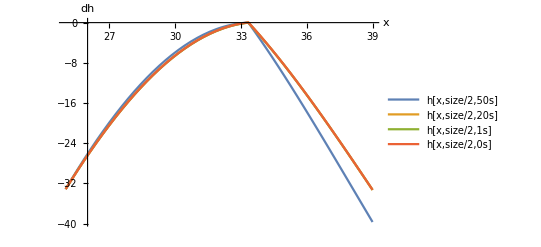

```mathematica
Plot[{scaleFun[plotFun[x,tMax],mintMax,maxtMax,tMax],scaleFun[plotFun[x,20000000],min20s,max20s,20000000],scaleFun[plotFun[x,1000000],min1s,max1s,1000000],scaleFun[plotFun[x,1],min0s,max0s,1]},{x,xMin,xMax},AxesLabel->{"x","dh"},PlotLegends->{"h[x,size/2,50s]","h[x,size/2,20s]","h[x,size/2,1s]","h[x,size/2,0s]"},PlotRange->Full]
```

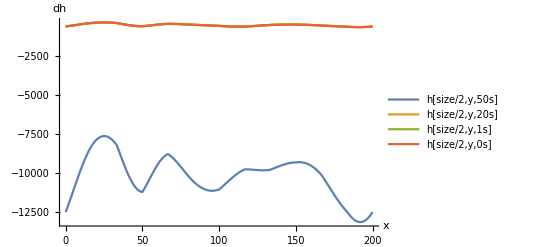

```mathematica
Plot[{scaleFunNotEntireDomain[plotFunYCut[y,tMax],min50s,max50s,50000000],scaleFunNotEntireDomain[plotFunYCut[y,20000000],min20s,max20s,20000000],scaleFunNotEntireDomain[plotFunYCut[y,1000000],min1s,max1s,1000000],scaleFunNotEntireDomain[plotFunYCut[y,1],min0s,max0s,1]},{y,0,200},AxesLabel->{"x","dh"},PlotLegends->{"h[size/2,y,50s]","h[size/2,y,20s]","h[size/2,y,1s]","h[size/2,y,0s]"},PlotRange->Full]
```

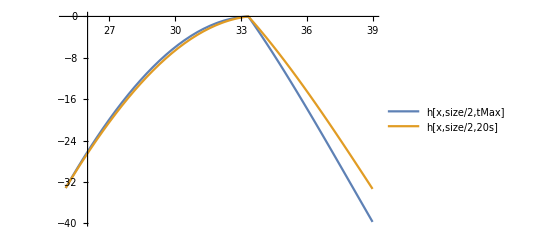

```mathematica
Plot[{scaleFun[plotFun[x,tMax],mintMax,maxtMax,tMax],scaleFun[plotFun[x,20000000],min20s,max20s,20000000]},{x,xMin,xMax},PlotLegends->{"h[x,size/2,tMax]","h[x,size/2,20s]"}]
```

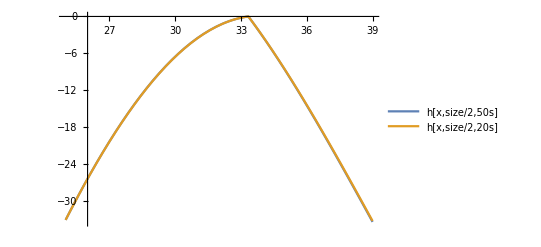

```mathematica
Plot[{scaleFun[plotFun[x,50000000],min50s,max50s,50000000],scaleFun[plotFun[x,20000000],min20s,max20s,20000000]},{x,xMin,xMax},PlotLegends->{"h[x,size/2,50s]","h[x,size/2,20s]"}]
```

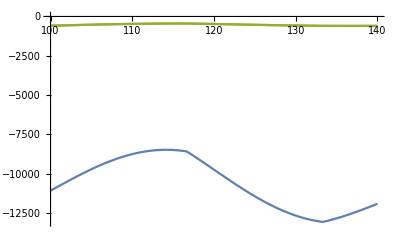

```mathematica
Plot[{scaleFunNotEntireDomain[plotFun[x,tMax],min50s,max50s,tMax],scaleFunNotEntireDomain[plotFun[x,20000000],min20s,max20s,20000000],scaleFunNotEntireDomain[plotFun[x,1],min0s,max0s,1]},{x,100,140}]
```

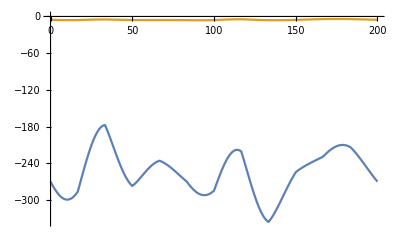

```mathematica
Plot[{ffun[x,100,tMax],ffun[x,100,20000000]},{x,0,200}]
```

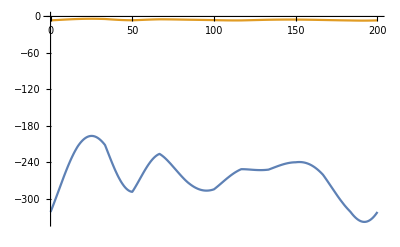

```mathematica
Plot[{ffun[100,y,tMax],ffun[100,y,20000000]},{y,0,200}]
```

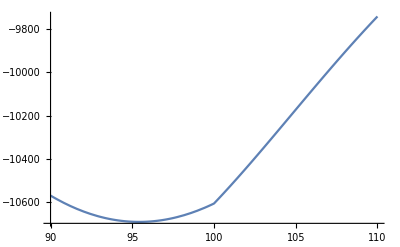

```mathematica
Plot[{scaleFun[plotFunYCut[y,tMax],min50s,max50s,tMax],scaleFun[plotFunYCut[y,20000000],min20s,max20s]},{y,90,110}]
```

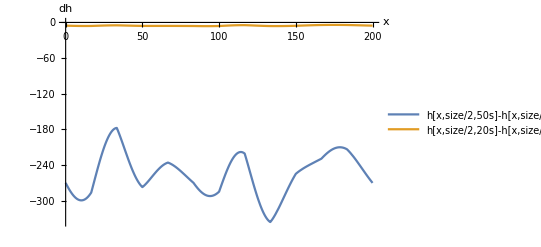

```mathematica
Plot[{diff[x,tMax],diff[x,20000000]},{x,0,size},AxesLabel->{"x","dh"},PlotLegends->{"h[x,size/2,50s]-h[x,size/2,0]","h[x,size/2,20s]-h[x,size/2,0]"}]
```

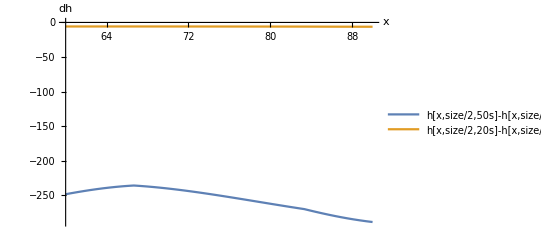

```mathematica
Plot[{diff[x,tMax],diff[x,20000000]},{x,60,90},AxesLabel->{"x","dh"},PlotLegends->{"h[x,size/2,50s]-h[x,size/2,0]","h[x,size/2,20s]-h[x,size/2,0]"}]
```

```mathematica
ffun[120,120,tMax]-ffun[120,120,0]
```

-257.333349167051

```mathematica
NMaximize[{plotFun[x,1],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
maxDegX = NMaximize[{RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]]/.{x->xVal,y->100,t->tMax},0≤xVal≤size},xVal,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
maxDegY = NMaximize[{RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]]/.{x->100,y->yVal,t->tMax},0≤yVal≤size},yVal,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
maxDegX
```

84.1293

```mathematica
maxDegY
```

82.686

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]]/.{x->70,y->70,t->0}
```

0.

```mathematica
Table[{xVal,{RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]]/.{x->xVal,y->100,t->50000000}}},{xVal,0,size}]
```

{{0,{10.726944493658}},{1,{12.5848759661}},{2,{12.214260520663}},{3,{11.77354958769}},{4,{11.27194490562}},{5,{10.7197095992}},{6,{10.12850846981}},{7,{9.511842630179}},{8,{8.885589140963}},{9,{8.268623420399}},{10,{7.6834113762}},{11,{7.156261129653}},{12,{6.716599128719}},{13,{6.394342292373}},{14,{6.214748343807}},{15,{6.191759603045}},{16,{6.3231458423654}},{17,{13.009823135973}},{18,{13.066804482772}},{19,{12.998392890594}},{20,{12.80890723337}},{21,{12.504356476308}},{22,{12.091969186794}},{23,{11.580005929296}},{24,{10.977780234545}},{25,{10.295866547245}},{26,{9.5465231388832}},{27,{8.7444204372573}},{28,{7.907859589284}},{29,{7.060810035458}},{30,{6.236259295767}},{31,{5.481259271116}},{32,{4.862403581358}},{33,{4.464327391706}},{34,{8.5260081796998}},{35,{8.9369142562005}},{36,{9.2554111965309}},{37,{9.4812265258972}},{38,{9.6167406025135}},{39,{9.6657911604288}},{40,{9.6329985280322}},{41,{9.5233828324113}},{42,{9.3421500245504}},{43,{9.0945785544049}},{44,{8.7859681301427}},{45,{8.4216286435527}},{46,{8.006897338937}},{47,{7.547179054043}},{48,{7.048010005005}},{49,{6.5151519459865}},{50,{5.9547329683138}},{51,{2.457822927131}},{52,{2.168130566737}},{53,{1.899442787882}},{54,{1.64636399914}},{55,{1.40529283176}},{56,{1.1750565314}},{57,{0.958244415266}},{58,{0.764369440305}},{59,{0.616582681443}},{60,{0.5562478836442}},{61,{0.612924778852}},{62,{0.762534655096}},{63,{0.96275122962}},{64,{1.186972781935}},{65,{1.421507422976}},{66,{1.658719096184}},{67,{1.964264866417}},{68,{2.265556968645}},{69,{2.544808397533}},{70,{2.798835732749}},{71,{3.024819145677}},{72,{3.220274383997}},{73,{3.383039632926}},{74,{3.511269911459}},{75,{3.603436661021}},{76,{3.65833242153}},{77,{3.67508192226}},{78,{3.653162374253}},{79,{3.592437848667}},{80,{3.493216172661}},{81,{3.356343227724}},{82,{3.183361802985}},{83,{2.976786303575}},{84,{7.048502435798}},{85,{6.481420493321}},{86,{5.8346685590346}},{87,{5.132315801892}},{88,{4.4096526221}},{89,{3.723917640446}},{90,{3.172702326885}},{91,{2.902940600092}},{92,{3.041521648478}},{93,{3.569224827162}},{94,{4.357544007835}},{95,{5.289854711219}},{96,{6.292663585078}},{97,{7.321386993824}},{98,{8.3468246064113}},{99,{9.3478886236748}},{100,{10.308026870604}},{101,{19.972476182132}},{102,{19.996207542402}},{103,{19.791744531268}},{104,{19.372310710787}},{105,{18.749784479567}},{106,{17.935216530424}},{107,{16.939371418032}},{108,{15.773296840248}},{109,{14.448938132241}},{110,{12.9798463976}},{111,{11.38210985157}},{112,{9.67586977711}},{113,{7.88851967818}},{114,{6.063420009753}},{115,{4.290296816099}},{116,{2.836276699872}},{117,{12.425985831253}},{118,{13.353140187033}},{119,{14.213019950793}},{120,{14.979648570227}},{121,{15.637057045822}},{122,{16.175255508882}},{123,{16.587836861798}},{124,{16.87055367078}},{125,{17.020476461681}},{126,{17.035508015423}},{127,{16.914125752136}},{128,{16.655281220771}},{129,{16.258420201954}},{130,{15.723609922627}},{131,{15.051778647892}},{132,{14.245094065836}},{133,{13.307539852114}},{134,{10.20331378136}},{135,{8.449599166163}},{136,{6.666662723797}},{137,{4.91454872817}},{138,{3.331205056952}},{139,{2.347433825103}},{140,{2.699555183683}},{141,{4.000955024138}},{142,{5.565728831759}},{143,{7.161453127812}},{144,{8.710331340072}},{145,{10.17699644417}},{146,{11.54130707188}},{147,{12.790300142584}},{148,{13.915197005919}},{149,{14.910023878015}},{150,{15.770840924241}},{151,{17.720997416165}},{152,{17.888841763079}},{153,{17.929031742113}},{154,{17.848429580432}},{155,{17.653426985325}},{156,{17.350039749392}},{157,{16.944005547101}},{158,{16.440882210681}},{159,{15.846144459629}},{160,{15.16527750998}},{161,{14.40386635101}},{162,{13.567679914835}},{163,{12.66275011476}},{164,{11.695447192559}},{165,{10.672555787805}},{166,{9.6013623885424}},{167,{7.807232639603}},{168,{6.521302354016}},{169,{5.276826124857}},{170,{4.11344107392}},{171,{3.104362928538}},{172,{2.400658201133}},{173,{2.229937412845}},{174,{2.620688542732}},{175,{3.317258776669}},{176,{4.112376829897}},{177,{4.911000946463}},{178,{5.671605218691}},{179,{6.374637440561}},{180,{7.010527088494}},{181,{7.574995997441}},{182,{8.0670565257825}},{183,{8.4880841018113}},{184,{9.744369072681}},{185,{9.730374615586}},{186,{9.712953965032}},{187,{9.702163025289}},{188,{9.70596241051}},{189,{9.7298854950998}},{190,{9.7768575834357}},{191,{9.8472018916952}},{192,{9.9388367111992}},{193,{10.04763299324}},{194,{10.1678754356}},{195,{10.292760884466}},{196,{10.414875436512}},{197,{10.52660978893}},{198,{10.620493174071}},{199,{10.689443695945}},{200,{10.726944493658}}}

```mathematica
Table[{xVal,{RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]]/.{x->xVal,y->100,t->50000000}}},{xVal,0,size}]
```

{{0,{10.726944493658}},{1,{12.5848759661}},{2,{12.214260520663}},{3,{11.77354958769}},{4,{11.27194490562}},{5,{10.7197095992}},{6,{10.12850846981}},{7,{9.511842630179}},{8,{8.885589140963}},{9,{8.268623420399}},{10,{7.6834113762}},{11,{7.156261129653}},{12,{6.716599128719}},{13,{6.394342292373}},{14,{6.214748343807}},{15,{6.191759603045}},{16,{6.3231458423654}},{17,{13.009823135973}},{18,{13.066804482772}},{19,{12.998392890594}},{20,{12.80890723337}},{21,{12.504356476308}},{22,{12.091969186794}},{23,{11.580005929296}},{24,{10.977780234545}},{25,{10.295866547245}},{26,{9.5465231388832}},{27,{8.7444204372573}},{28,{7.907859589284}},{29,{7.060810035458}},{30,{6.236259295767}},{31,{5.481259271116}},{32,{4.862403581358}},{33,{4.464327391706}},{34,{8.5260081796998}},{35,{8.9369142562005}},{36,{9.2554111965309}},{37,{9.4812265258972}},{38,{9.6167406025135}},{39,{9.6657911604288}},{40,{9.6329985280322}},{41,{9.5233828324113}},{42,{9.3421500245504}},{43,{9.0945785544049}},{44,{8.7859681301427}},{45,{8.4216286435527}},{46,{8.006897338937}},{47,{7.547179054043}},{48,{7.048010005005}},{49,{6.5151519459865}},{50,{5.9547329683138}},{51,{2.457822927131}},{52,{2.168130566737}},{53,{1.899442787882}},{54,{1.64636399914}},{55,{1.40529283176}},{56,{1.1750565314}},{57,{0.958244415266}},{58,{0.764369440305}},{59,{0.616582681443}},{60,{0.5562478836442}},{61,{0.612924778852}},{62,{0.762534655096}},{63,{0.96275122962}},{64,{1.186972781935}},{65,{1.421507422976}},{66,{1.658719096184}},{67,{1.964264866417}},{68,{2.265556968645}},{69,{2.544808397533}},{70,{2.798835732749}},{71,{3.024819145677}},{72,{3.220274383997}},{73,{3.383039632926}},{74,{3.511269911459}},{75,{3.603436661021}},{76,{3.65833242153}},{77,{3.67508192226}},{78,{3.653162374253}},{79,{3.592437848667}},{80,{3.493216172661}},{81,{3.356343227724}},{82,{3.183361802985}},{83,{2.976786303575}},{84,{7.048502435798}},{85,{6.481420493321}},{86,{5.8346685590346}},{87,{5.132315801892}},{88,{4.4096526221}},{89,{3.723917640446}},{90,{3.172702326885}},{91,{2.902940600092}},{92,{3.041521648478}},{93,{3.569224827162}},{94,{4.357544007835}},{95,{5.289854711219}},{96,{6.292663585078}},{97,{7.321386993824}},{98,{8.3468246064113}},{99,{9.3478886236748}},{100,{10.308026870604}},{101,{19.972476182132}},{102,{19.996207542402}},{103,{19.791744531268}},{104,{19.372310710787}},{105,{18.749784479567}},{106,{17.935216530424}},{107,{16.939371418032}},{108,{15.773296840248}},{109,{14.448938132241}},{110,{12.9798463976}},{111,{11.38210985157}},{112,{9.67586977711}},{113,{7.88851967818}},{114,{6.063420009753}},{115,{4.290296816099}},{116,{2.836276699872}},{117,{12.425985831253}},{118,{13.353140187033}},{119,{14.213019950793}},{120,{14.979648570227}},{121,{15.637057045822}},{122,{16.175255508882}},{123,{16.587836861798}},{124,{16.87055367078}},{125,{17.020476461681}},{126,{17.035508015423}},{127,{16.914125752136}},{128,{16.655281220771}},{129,{16.258420201954}},{130,{15.723609922627}},{131,{15.051778647892}},{132,{14.245094065836}},{133,{13.307539852114}},{134,{10.20331378136}},{135,{8.449599166163}},{136,{6.666662723797}},{137,{4.91454872817}},{138,{3.331205056952}},{139,{2.347433825103}},{140,{2.699555183683}},{141,{4.000955024138}},{142,{5.565728831759}},{143,{7.161453127812}},{144,{8.710331340072}},{145,{10.17699644417}},{146,{11.54130707188}},{147,{12.790300142584}},{148,{13.915197005919}},{149,{14.910023878015}},{150,{15.770840924241}},{151,{17.720997416165}},{152,{17.888841763079}},{153,{17.929031742113}},{154,{17.848429580432}},{155,{17.653426985325}},{156,{17.350039749392}},{157,{16.944005547101}},{158,{16.440882210681}},{159,{15.846144459629}},{160,{15.16527750998}},{161,{14.40386635101}},{162,{13.567679914835}},{163,{12.66275011476}},{164,{11.695447192559}},{165,{10.672555787805}},{166,{9.6013623885424}},{167,{7.807232639603}},{168,{6.521302354016}},{169,{5.276826124857}},{170,{4.11344107392}},{171,{3.104362928538}},{172,{2.400658201133}},{173,{2.229937412845}},{174,{2.620688542732}},{175,{3.317258776669}},{176,{4.112376829897}},{177,{4.911000946463}},{178,{5.671605218691}},{179,{6.374637440561}},{180,{7.010527088494}},{181,{7.574995997441}},{182,{8.0670565257825}},{183,{8.4880841018113}},{184,{9.744369072681}},{185,{9.730374615586}},{186,{9.712953965032}},{187,{9.702163025289}},{188,{9.70596241051}},{189,{9.7298854950998}},{190,{9.7768575834357}},{191,{9.8472018916952}},{192,{9.9388367111992}},{193,{10.04763299324}},{194,{10.1678754356}},{195,{10.292760884466}},{196,{10.414875436512}},{197,{10.52660978893}},{198,{10.620493174071}},{199,{10.689443695945}},{200,{10.726944493658}}}

```mathematica
Table[{xVal,{RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]]/.{x->xVal,y->100,t->tMax}}},{xVal,0,size}]
```

{{0,{76.7652276461018}},{1,{79.8620007128169}},{2,{79.2716170181687}},{3,{78.4962809472653}},{4,{77.4897148011681}},{5,{76.1868669960488}},{6,{74.500462397314}},{7,{72.32668218206}},{8,{69.588236053501}},{9,{66.391470623402}},{10,{63.391984441924}},{11,{62.009457779828}},{12,{63.261818530599}},{13,{66.316102619119}},{14,{69.682887170423}},{15,{72.6023788105797}},{16,{74.9311900069891}},{17,{84.05348908522251}},{18,{84.12266973587287}},{19,{84.11770031944797}},{20,{84.04291910830079}},{21,{83.89806494298612}},{22,{83.67853403546369}},{23,{83.37499425558701}},{24,{82.972306629019}},{25,{82.4475348193238}},{26,{81.7666045406234}},{27,{80.8788746187675}},{28,{79.7085837783711}},{29,{78.142569070962}},{30,{76.0186890305596}},{31,{73.1468713132105}},{32,{69.507856221987}},{33,{65.988214539189}},{34,{81.4880108954428}},{35,{81.8759448820324}},{36,{82.1265081364302}},{37,{82.2648803091455}},{38,{82.3066984279221}},{39,{82.2606268155474}},{40,{82.1298687391313}},{41,{81.9129110387839}},{42,{81.6036800673306}},{43,{81.191186280403}},{44,{80.6586592616534}},{45,{79.9821310732488}},{46,{79.1284518794709}},{47,{78.0529554204586}},{48,{76.6978536923948}},{49,{74.9951159128733}},{50,{72.8849934632971}},{51,{72.09993583511}},{52,{72.7833158352}},{53,{73.221408353988}},{54,{73.431533798802}},{55,{73.427907037746}},{56,{73.217002088821}},{57,{72.7961163957616}},{58,{72.1527817655416}},{59,{71.2643045745069}},{60,{70.0976070008223}},{61,{68.6105471626827}},{62,{66.757871464409}},{63,{64.509110690495}},{64,{61.892946604074}},{65,{59.087314636142}},{66,{56.544139939262}},{67,{57.643274571706}},{68,{60.976914483675}},{69,{63.554988802444}},{70,{65.557302585704}},{71,{67.121638020599}},{72,{68.348147927004}},{73,{69.308723958678}},{74,{70.055010964094}},{75,{70.624239136587}},{76,{71.043259175519}},{77,{71.331287971601}},{78,{71.501764593857}},{79,{71.563594235369}},{80,{71.521964199043}},{81,{71.378851362889}},{82,{71.1332975394795}},{83,{70.7815012907031}},{84,{75.7967995905943}},{85,{75.1660605234584}},{86,{74.335410325391}},{87,{73.272503345855}},{88,{71.935415612636}},{89,{70.275328083022}},{90,{68.247184878463}},{91,{65.839967655861}},{92,{63.146724329876}},{93,{60.485940157458}},{94,{58.494852811418}},{95,{57.928451095379}},{96,{59.066101407249}},{97,{61.421353877416}},{98,{64.219498113245}},{99,{66.913921599512}},{100,{69.268126610385}},{101,{82.174566537617}},{102,{82.0635738246755}},{103,{81.8438125189843}},{104,{81.5063027348627}},{105,{81.0334097804588}},{106,{80.396478230217}},{107,{79.5516286066466}},{108,{78.4330044502935}},{109,{76.9429937757065}},{110,{74.941941558239}},{111,{72.255485353251}},{112,{68.781787195098}},{113,{64.949727856904}},{114,{62.5713556369}},{115,{63.749786789063}},{116,{67.456311296422}},{117,{83.4558799330338}},{118,{83.6419563221207}},{119,{83.7451319074063}},{120,{83.7762096748922}},{121,{83.7410115052509}},{122,{83.641344289294}},{123,{83.4754065903873}},{124,{83.2377305139025}},{125,{82.9186613095992}},{126,{82.5032836924555}},{127,{81.9695896614532}},{128,{81.2855280256266}},{129,{80.4043827541214}},{130,{79.2578257809433}},{131,{77.7467141545786}},{132,{75.7346002426481}},{133,{73.071651639539}},{134,{76.135838559261}},{135,{76.706649565254}},{136,{77.3637349094258}},{137,{78.0338307598265}},{138,{78.6729002974271}},{139,{79.2582231893181}},{140,{79.7803770329531}},{141,{80.2373825849458}},{142,{80.6310059616303}},{143,{80.9646039156357}},{144,{81.2419322886223}},{145,{81.4665127296846}},{146,{81.6413063561751}},{147,{81.7685465744296}},{148,{81.8496458415126}},{149,{81.885126601689}},{150,{81.8745454673048}},{151,{80.3644519701806}},{152,{80.1369680022033}},{153,{79.852194225574}},{154,{79.5042781364825}},{155,{79.085971132115}},{156,{78.588267493814}},{157,{77.999989290088}},{158,{77.307299041306}},{159,{76.49313464766}},{160,{75.536588084136}},{161,{74.412308537484}},{162,{73.090136831619}},{163,{71.535436779658}},{164,{69.711093642393}},{165,{67.583056367139}},{166,{65.132681446427}},{167,{71.726233186549}},{168,{70.134811264486}},{169,{68.360016310586}},{170,{66.430986849722}},{171,{64.415875694541}},{172,{62.434880696054}},{173,{60.660661252304}},{174,{59.29132887391}},{175,{58.49257384931}},{176,{58.334725837739}},{177,{58.768642035505}},{178,{59.65788837872}},{179,{60.838658259076}},{180,{62.167568525072}},{181,{63.541640225005}},{182,{64.897360190048}},{183,{66.200972625846}},{184,{72.050829712109}},{185,{72.325470659531}},{186,{72.670478751024}},{187,{73.075749083197}},{188,{73.5245630500874}},{189,{73.9968442266341}},{190,{74.4722726163493}},{191,{74.932540193592}},{192,{75.3625217521}},{193,{75.750514027208}},{194,{76.087858331614}},{195,{76.368252625877}},{196,{76.586970224637}},{197,{76.7401041945495}},{198,{76.8238807295728}},{199,{76.8340365038866}},{200,{76.7652276461018}}}